```mathematica
cells = {{0,0}}
```

{{0,0}}

```mathematica
adds = {{1,0},{0,1},{-1,0},{0,-1}}
```

{{1,0},{0,1},{-1,0},{0,-1}}

```mathematica
NextCells[cells_List,adds_:{{1,0},{0,1},{-1,0},{0,-1}}]:=Complement[Union[Catenate[Outer[Plus,cells,adds,1]]],cells]
NextCellsMoore[cells_List] := NextCells[cells,Tuples[{-1,0,1},2]]
```

```mathematica
TotalisticPruneQ[{rn_,offsets_},state_,newpos_]:=With[{
rulevec=Reverse[IntegerDigits[rn,2, Length[offsets]]]
},rulevec[[Total[Boole[MemberQ[state,newpos+#]&/@offsets]]]]==1]
```

```mathematica
PlotCells[cells_,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells-Min[cells]+1->1],{Max[cells]-Min[cells]+1,Max[cells]-Min[cells]+1}],opts]
```

```mathematica
PlotCells[cells_,n_Integer,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells+Ceiling[n/2]->1],{n,n}],opts]
```

```mathematica
ArrayPlot[SparseArray[Thread[{{0,0},{1,1}}+Ceiling[10/2]-> 1],{10,10}] // Echo]
```

SparseArray[…]

-Graphics-

```mathematica
NextCells[cells]
```

{{-1,0},{0,-1},{0,1},{1,0}}

{{0,0}}

{{-1,0},{0,0}}

{{0,-1},{0,0}}

{{0,0},{0,1}}

{{0,0},{1,0}}

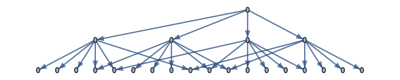

```mathematica
g=NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s // Echo]],{{{0,0}}},2]
```

```mathematica
{{0,1}}
```

{{0,1}}

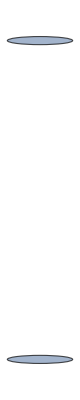

```mathematica
Graph[{{1,1},{1,2}},{}]
```

```mathematica
PlotCells[{{0,0},{1,1}},2]
```

-Graphics-

```mathematica
Manipulate[NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s]],{{{0,0}}},n], {n,0,10, 1}]
```

```mathematica
Manipulate[Graph[NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s]],{{{0,0}}},n]], {n,0,10, 1}]
```

TotalisticManipulate general method

```mathematica
TotalisticManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], Union[Append[s,#]],Nothing]&/@NextCells[s]],{initial},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,n+4,ImageSize->15],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
],{n,0,10,1}]
```

```mathematica
TotalisticManipulate[242, {{0,0},{1,1},{1,0},{1,-1},{2,-1}}, True]
```

Introducing canonicalization (for translation):
(convert list of cells to list of cells distanced from minimum coordinates among cells)

```mathematica
CellCanonicalize[state_]:=With[{m=Min/@Transpose[state]},#-m&/@state]
```

```mathematica
CellCanonicalize[{{0,0},{1,-2},{1,-1},{1,0},{1,1},{2,-1}}]
```

{{0,2},{1,0},{1,1},{1,2},{1,3},{2,1}}

```mathematica
TotalisticCanonManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], CellCanonicalize[Union[Append[s,#]]],Nothing]&/@NextCells[s]],{CellCanonicalize[initial]},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,ImageSize->15, Mesh->True],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
],{n,0,10,1}]
```

```mathematica
TotalisticCanonManipulate[rule_:242, initial_:{{0, 0}}, usePlotCells_:False] := 
	Manipulate[
		With[{
		g = NestGraph[Function[s, (If[TotalisticPruneQ[{rule, Tuples[{-1, 0, 1}, 2]}, s, #1],
CellCanonicalize[Union[Append[s, #1]]], Nothing] & ) /@ NextCells[s]], 
	{CellCanonicalize[initial]}, n]}, 
    Graph[g, VertexLabels -> (#1 -> If[usePlotCells, PlotCells[#1, ImageSize -> 15, Mesh -> True], 
          ""] & ) /@ VertexList[g], GraphLayout -> "LayeredDigraphEmbedding", 
     AspectRatio -> 1/2]], {n, 0, 10, 1}]
```

```mathematica
TotalisticCanonManipulate[242, {{0,0},{1,-1}}, True]
```

```mathematica
TotalisticCanonManipulate[242, {{0,0},{-1,1},{0,1},{1,1}}, True]
```

Now with rotational canonicalization

```mathematica
CellCanonicalizeRotations[cells_]:=Module[{dim,mins,positive,array,canonarray},dim=Max[#]-Min[#]+1&/@Transpose[cells];
mins=Min/@Transpose[cells];
positive=#-mins+1&/@cells;
array=ReplacePart[ConstantArray[0,dim],positive->1];
canonarray=First[Sort[ResourceFunction["ArrayRotations"][ResourceFunction["ArrayCrop"][array]]]];
Position[canonarray,1]-1]
```

```mathematica
TotalisticFullCanonManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], CellCanonicalizeRotations[Union[Append[s,#]]],Nothing]&/@NextCellsMoore[s]],{CellCanonicalizeRotations[initial]},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,ImageSize->15, Mesh->True],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
],{n,0,10,1}]
```

```mathematica
TotalisticCanonManipulate[1, {{0,0}}, True]
```

TotalisticCanonManipulate[1,{{0,0}},True]

```mathematica
TotalisticFullCanonManipulate[242, {{0,0},{1,1}}, True]
```

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer::heads will be suppressed during this calculation.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

General::stop: Further output of If::argbu will be suppressed during this calculation.

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

General::stop: Further output of SparseArray::posd will be suppressed during this calculation.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer::heads will be suppressed during this calculation.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

General::stop: Further output of If::argbu will be suppressed during this calculation.

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

General::stop: Further output of SparseArray::posd will be suppressed during this calculation.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

#### Halt find

```mathematica
(* Computes list of states generated from 1 given state - list of cells *)
NextStates[rule_Integer, state_List] :=With[{neigh = Tuples[{-1,0,1},2]},If[TotalisticPruneQ[{rule,neigh},state,#],CellCanonicalizeRotations@Union@Append[state,#],Nothing]&/@NextCells[state,neigh]]
```

```mathematica
(* Computes list of all (flattened) states generated from list of states *)
NextStatesList[rule_Integer, states_List] := Union@Flatten[NextStates[rule, #]& /@ states,1]
```

```mathematica
HaltFindRaw[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[NextStatesList[rule, #]&, {CellCanonicalizeRotations@initial}, True&, 1, maxn]
```

#### Halt find with halt states information

```mathematica
NextStatesListWithInfo[rule_Integer, states_List] := {Union@Flatten[#,1],states[[Flatten@Position[#,{}]]]}&@(NextStates[rule, #]& /@ states)
```

```mathematica
HaltFind[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[NextStatesListWithInfo[rule, First[#]]&, {{CellCanonicalizeRotations@initial},{}}, Last[#]=={}&, 1, maxn]
```

```mathematica
HaltFind[242,{{0,0}},5] // Last
```

{{{0,0}}}

```mathematica
MinNeigh[rule_Integer]:=FirstPosition[Reverse@IntegerDigits[rule,2,8],1]//First
```

```mathematica
(*TODO: MinimalInitial[rule_Integer] := *)
```

```mathematica
PlotBinaryGroupsHalt[bit_Integer,initial_List,maxn_Integer] := ParallelTable[Labeled[PlotCells[#,ImageSize->30,Mesh->True]&/@Last@HaltFind[rn, initial,maxn],rn],{rn,Select[Range@255,MinNeigh[#]==bit&]}]
```

```mathematica
PlotBinaryGroupsOnlyHalt[bit_Integer,initial_List,maxn_Integer] := Select[PlotBinaryGroupsHalt[bit,initial,maxn],#[[1]]=!={}&]
```

## Exploring bit groups

#### Definition: k-Bit rule: a rule where the bit k is the lower bit set, i.e., system admit cells with exactly k neighbors and possibly more (but not less). is the set of k-bit rules.

```mathematica
data = Function[bit,Select[Range@255,MinNeigh[#]==bit&]] /@ Range@8 ;
formattedData = Transpose @{Range@Length@data,StringJoin["(#",ToString@Length@#,"): ",StringRiffle[ToString/@#,","]]&/@ data};
Print[Grid[Prepend[formattedData,{"Bit","Bit Rules Set"}],Frame->All,Alignment->Left]];
```

Bit | Bit Rules Set
1 | (#128): 1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215,217,219,221,223,225,227,229,231,233,235,237,239,241,243,245,247,249,251,253,255
2 | (#64): 2,6,10,14,18,22,26,30,34,38,42,46,50,54,58,62,66,70,74,78,82,86,90,94,98,102,106,110,114,118,122,126,130,134,138,142,146,150,154,158,162,166,170,174,178,182,186,190,194,198,202,206,210,214,218,222,226,230,234,238,242,246,250,254
3 | (#32): 4,12,20,28,36,44,52,60,68,76,84,92,100,108,116,124,132,140,148,156,164,172,180,188,196,204,212,220,228,236,244,252
4 | (#16): 8,24,40,56,72,88,104,120,136,152,168,184,200,216,232,248
5 | (#8): 16,48,80,112,144,176,208,240
6 | (#4): 32,96,160,224
7 | (#2): 64,192
8 | (#1): 128

#### Remarks:

### 4 connectivity:

#### 1-Bit rules never halt

Proof: Let s be any given state (collection of cells). There will be a set of cells with higher horizontal coordinate. Let p be the coordinates of the cell from this set with higher vertical coordinate. The cells at positions p+{-1,1} and p+{1,1} will be unset, so the cell at p+{0,1} will have exactly one neighbor. So the system can grow with it.

#### Non 1-Bit rules always halt

Proof: Let s be any given state (collection of cells). Let r be any rectangle that contains all cells from s. A cell outside r will have, at most, 1 neighbors cell inside rUs. It is then impossible to add a cell from outside, and so the system will halt eventually
-Graphics-

### 8 connectivity:

#### 1-Bit rules never halt.

Proof: Let s be any given state (collection of cells). There will be a set of cells with higher horizontal coordinate. Let p be the coordinates of the cell from this set with higher vertical coordinate. The cell at position p+{1,1} will have exactly one neighbor. So the system can grow with it.
-Graphics-

#### ()-Bit rules always halt.

-Graphics-
Proof: Let s be any given state (collection of cells). Let r be any rectangle that contains all cells from s. A cell outside r will have, at most, 3 neighbors cell inside rUs. It is then impossible to add a cell from outside, and so the system will halt eventually

#### Left with 2-Bit and 3-Bit

## Simulations

```mathematica
PlotBinaryGroupsHalt[1,{{0,0}},8]
```

{{}1,{}3,{}5,{}7,{}9,{}11,{}13,{}15,{}17,{}19,{}21,{}23,{}25,{}27,{}29,{}31,{}33,{}35,{}37,{}39,{}41,{}43,{}45,{}47,{}49,{}51,{}53,{}55,{}57,{}59,{}61,{}63,{}65,{}67,{}69,{}71,{}73,{}75,{}77,{}79,{}81,{}83,{}85,{}87,{}89,{}91,{}93,{}95,{}97,{}99,{}101,{}103,{}105,{}107,{}109,{}111,{}113,{}115,{}117,{}119,{}121,{}123,{}125,{}127,{}129,{}131,{}133,{}135,{}137,{}139,{}141,{}143,{}145,{}147,{}149,{}151,{}153,{}155,{}157,{}159,{}161,{}163,{}165,{}167,{}169,{}171,{}173,{}175,{}177,{}179,{}181,{}183,{}185,{}187,{}189,{}191,{}193,{}195,{}197,{}199,{}201,{}203,{}205,{}207,{}209,{}211,{}213,{}215,{}217,{}219,{}221,{}223,{}225,{}227,{}229,{}231,{}233,{}235,{}237,{}239,{}241,{}243,{}245,{}247,{}249,{}251,{}253,{}255}

```mathematica
TotalisticFullCanonManipulate[2,{{0,0},{1,1}}, True]
```

```mathematica
PlotBinaryGroupsHalt[2,{{0,0},{1,1}},9]
```

{{}2,{}6,{}10,{}14,{-Graphics-}18,{}22,{-Graphics-}26,{}30,{}34,{}38,{}42,{}46,{-Graphics-}50,{}54,{-Graphics-}58,{}62,{}66,{}70,{}74,{}78,{-Graphics-}82,{}86,{-Graphics-}90,{}94,{}98,{}102,{}106,{}110,{-Graphics-}114,{}118,{-Graphics-}122,{}126,{}130,{}134,{}138,{}142,{-Graphics-}146,{}150,{-Graphics-}154,{}158,{}162,{}166,{}170,{}174,{-Graphics-}178,{}182,{-Graphics-}186,{}190,{}194,{}198,{}202,{}206,{-Graphics-}210,{}214,{-Graphics-}218,{}222,{}226,{}230,{}234,{}238,{-Graphics-}242,{}246,{-Graphics-}250,{}254}

-3Bit rules:
- Initial
	Always halt, since a square with size 2 has all neighbours requiring less than 
- PlotCells[{{0,0},{}}]

```mathematica
-3 Bit (rules:-Initial -Graphics-)
```

```mathematica
PlotCells[Can]
```

```mathematica
MinimalInitials[bit_Integer] := Tuples[Range[bit],2] // Subsets[#,{bit}]& // (CellCanonicalizeRotations/@#)& // Union
```

```mathematica
PlotCells[#,ImageSize->30,Mesh->True]&/@ MinimalInitials[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[1]],17]
```

{{-Graphics-}4,{}12,{-Graphics-}20,{}28,{-Graphics-}36,{}44,{-Graphics-}52,{}60,{-Graphics-}68,{}76,{-Graphics-}84,{}92,{-Graphics-}100,{}108,{-Graphics-}116,{}124,{-Graphics-}132,{}140,{-Graphics-}148,{}156,{-Graphics-}164,{}172,{-Graphics-}180,{}188,{-Graphics-}196,{}204,{-Graphics-}212,{}220,{-Graphics-}228,{}236,{-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[2]],17]
```

{{-Graphics-}4,{-Graphics-}12,{-Graphics-}20,{-Graphics-}28,{-Graphics-}36,{-Graphics-}44,{-Graphics-}52,{-Graphics-}60,{-Graphics-}68,{-Graphics-}76,{-Graphics-}84,{-Graphics-}92,{-Graphics-}100,{-Graphics-}108,{-Graphics-}116,{-Graphics-}124,{-Graphics-}132,{-Graphics-}140,{-Graphics-}148,{-Graphics-}156,{-Graphics-}164,{-Graphics-}172,{-Graphics-}180,{-Graphics-}188,{-Graphics-}196,{-Graphics-}204,{-Graphics-}212,{-Graphics-}220,{-Graphics-}228,{-Graphics-}236,{-Graphics-}244,{-Graphics-}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[3]],17]
```

{{-Graphics-}4,{}12,{-Graphics-}20,{}28,{-Graphics-}36,{}44,{-Graphics-}52,{}60,{-Graphics-}68,{}76,{-Graphics-}84,{}92,{-Graphics-}100,{}108,{-Graphics-}116,{}124,{-Graphics-}132,{}140,{-Graphics-}148,{}156,{-Graphics-}164,{}172,{-Graphics-}180,{}188,{-Graphics-}196,{}204,{-Graphics-}212,{}220,{-Graphics-}228,{}236,{-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[4]],17]
```

{{-Graphics-}4,{}12,{-Graphics-}20,{}28,{-Graphics-}36,{}44,{-Graphics-}52,{}60,{-Graphics-}68,{}76,{-Graphics-}84,{}92,{-Graphics-}100,{}108,{-Graphics-}116,{}124,{-Graphics-}132,{}140,{-Graphics-}148,{}156,{-Graphics-}164,{}172,{-Graphics-}180,{}188,{-Graphics-}196,{}204,{-Graphics-}212,{}220,{-Graphics-}228,{}236,{-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[5]],17]
```

{{-Graphics-}4,{}12,{-Graphics-}20,{}28,{-Graphics-}36,{}44,{-Graphics-}52,{}60,{-Graphics-}68,{}76,{-Graphics-}84,{}92,{-Graphics-}100,{}108,{-Graphics-}116,{}124,{-Graphics-}132,{}140,{-Graphics-}148,{}156,{-Graphics-}164,{}172,{-Graphics-}180,{}188,{-Graphics-}196,{}204,{-Graphics-}212,{}220,{-Graphics-}228,{}236,{-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[6]],17]
```

{{}4,{}12,{}20,{}28,{}36,{}44,{}52,{}60,{}68,{}76,{}84,{}92,{}100,{}108,{}116,{}124,{}132,{}140,{}148,{}156,{}164,{}172,{}180,{}188,{}196,{}204,{}212,{}220,{}228,{}236,{}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[7]],17]
```

{{-Graphics-,-Graphics-}4,{}12,{-Graphics-,-Graphics-,-Graphics-}20,{}28,{-Graphics-,-Graphics-}36,{}44,{-Graphics-,-Graphics-,-Graphics-}52,{}60,{-Graphics-,-Graphics-}68,{}76,{-Graphics-,-Graphics-,-Graphics-}84,{}92,{-Graphics-,-Graphics-}100,{}108,{-Graphics-,-Graphics-,-Graphics-}116,{}124,{-Graphics-,-Graphics-}132,{}140,{-Graphics-,-Graphics-,-Graphics-}148,{}156,{-Graphics-,-Graphics-}164,{}172,{-Graphics-,-Graphics-,-Graphics-}180,{}188,{-Graphics-,-Graphics-}196,{}204,{-Graphics-,-Graphics-,-Graphics-}212,{}220,{-Graphics-,-Graphics-}228,{}236,{-Graphics-,-Graphics-,-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[8]],17]
```

{{-Graphics-}4,{-Graphics-}12,{-Graphics-}20,{-Graphics-}28,{-Graphics-}36,{-Graphics-}44,{-Graphics-}52,{-Graphics-}60,{-Graphics-}68,{-Graphics-}76,{-Graphics-}84,{-Graphics-}92,{-Graphics-}100,{-Graphics-}108,{-Graphics-}116,{-Graphics-}124,{-Graphics-}132,{-Graphics-}140,{-Graphics-}148,{-Graphics-}156,{-Graphics-}164,{-Graphics-}172,{-Graphics-}180,{-Graphics-}188,{-Graphics-}196,{-Graphics-}204,{-Graphics-}212,{-Graphics-}220,{-Graphics-}228,{-Graphics-}236,{-Graphics-}244,{-Graphics-}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[9]],17]
```

{{}4,{}12,{}20,{}28,{}36,{}44,{}52,{}60,{}68,{}76,{}84,{}92,{}100,{}108,{}116,{}124,{}132,{}140,{}148,{}156,{}164,{}172,{}180,{}188,{}196,{}204,{}212,{}220,{}228,{}236,{}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[10]],17]
```

{{-Graphics-,-Graphics-}4,{}12,{-Graphics-,-Graphics-,-Graphics-}20,{}28,{-Graphics-,-Graphics-}36,{}44,{-Graphics-,-Graphics-,-Graphics-}52,{}60,{-Graphics-,-Graphics-}68,{}76,{-Graphics-,-Graphics-,-Graphics-}84,{}92,{-Graphics-,-Graphics-}100,{}108,{-Graphics-,-Graphics-,-Graphics-}116,{}124,{-Graphics-,-Graphics-}132,{}140,{-Graphics-,-Graphics-,-Graphics-}148,{}156,{-Graphics-,-Graphics-}164,{}172,{-Graphics-,-Graphics-,-Graphics-}180,{}188,{-Graphics-,-Graphics-}196,{}204,{-Graphics-,-Graphics-,-Graphics-}212,{}220,{-Graphics-,-Graphics-}228,{}236,{-Graphics-,-Graphics-,-Graphics-}244,{}252}

```mathematica
TotalisticFullCanonManipulate[76,{{0,0},{0,1},{1,2}}, True]
```

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

Outer::heads: Heads List and CellCanonicalizeRotations at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer::heads will be suppressed during this calculation.

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

General::stop: Further output of If::argbu will be suppressed during this calculation.

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

SparseArray::posd: The left-hand side of 1→1 in {1→1} is not a position or a pattern that will match the position of an element in an array with dimensions {1,1}.

General::stop: Further output of SparseArray::posd will be suppressed during this calculation.

ArrayPlot::mat: Argument SparseArray[1→1,{1,1}] at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
PlotCells[{{0,0},{1,1},{1,0},{1,-1}},ImageSize->30,Mesh->True]
```

-Graphics-

## Misc...

```mathematica
(*2 sequentiall operations to SOW in halting states (Reap around everything)*)
If[halt_test, Sow[state]];state
```

state

```mathematica
HaltLeadTestState = {{0,0},{-1,1},{-2,2},{0,1},{-1,2},{1,1},{0,2}};
HaltTestState = Append[HaltLeadTestState, {-1,3}];
PlotCells[#,ImageSize->30,Mesh->True]&/@ {HaltLeadTestState,HaltTestState}
```

{-Graphics-,-Graphics-}